# Post Processing

This notebook is used to extract collapse rate from the raw thermal collapse data. 

Raw data is saved in ParentDirectory[]<>“data/thermal-collapse-data/...” where files are named
 
“topological_charge_during_relaxation(dynamics)_*”
“energy_during_relaxation(dynamics)_*”
“effective_size_during_relaxation(dynamics)_*”
“spin_field_after_relaxation(dynamics)_*”

Modifier ‘relaxation’ refers to data acquired during T=0 initial skyrmion relaxation, while ‘dynamics’ refers to data acquired during thermal collapse computation. Suffixes of filenames are parameter values followed by a timestamp. 

In order to extract collapse rate and energy barrier, need to process the topological charge data to determine the collapse time for various temperatures and fit the data to an exponential. 

To save time, it is useful to collect collapse times from all data runs and save them to their respective files in the folder “processed-collapse-times”

All necessary functions in this notebook are Initialization cells, which can be evaluate with Evaluation->Evaluate Initialization Cells

```mathematica
SetDirectory[NotebookDirectory[]];
plotSize=1000;

SetOptions[{MatrixPlot,ListVectorPlot},ImageSize->plotSize,ImagePadding->{{50,70},{50,50}},LabelStyle->{Directive["Times",14,Black],FontFamily->"Times"}];
SetOptions[{ListPlot,ListLogPlot,ListLogLogPlot,Plot,LogPlot,LogLogPlot,Histogram},Frame->True,AspectRatio->1/GoldenRatio,ImageSize->plotSize,LabelStyle->{Directive["Times",18,Black],FontFamily->"Times",ImagePadding->{{100,100},{100,100}}}];
```

Functions

```mathematica
(* 

Input: dirPrefix = directory where data is stored, T = temperature, H = external field, DMI = Dzyaloshinskii-Moraya Interaction, tfree = free evolution time from thermal collapse script. ;

Sample inputs: dirPrefix = ParentDirectory[]<>"/data/t-collapse-data", T = 0.1, H = -0.0014, DMI = 0.02, tfree = 2.0;

Output: collapseResults = list containing temperature and times at which collapse occured {T1, {t1,t2,..},T2,{t1,t2,..},...} ;

*)
getCollapseTimes[dirPrefix_,T_,H_,DMI_,ED_,PMA_]:=
Block[{chargeList,pos,posList={},i},

	(* Get data for all the data runs at this temperature *)
chargeList = ToExpression@Import[
dirPrefix<>"_T="<>ToString[T]<>"_H="<>ToString[H]<>"_DMI="<>ToString[DMI]<>
"_DDI="<>ToString[ED]<>"_PMA="<>ToString[PMA]<>"_*.h5",
"Data"][[All,1]];
	
Do[

(* Get the position where the topological charge drops *)
pos=Flatten[Position[Abs[chargeList[[i]]],_?(#<0.1&)]];

(* If there's more than 1 point where charge is close to zero, get the first one *)
If[Length[pos] >1, AppendTo[posList,First[pos]], AppendTo[posList,pos]],

{i,1,Length[chargeList]}];
	
(* Replace all empty lists with zero (empty means collapse did not occur)*)
Flatten[posList/.{{}->0}]

]
```

```mathematica
(*

Determines Γ from the list of collapse times ;

Input: nested list of collapse times at various temperatures. {T1, {t1,t2,..},T2,{t1,t2,..},...} ;
Output: proccessed list of temperaure and collapse rate {1/T, Γ};

For explanation of extraction of escape rate from collapse times see: 
D.A.Garanin, Uniform and nonuniform thermal switching of magnetic particles. Phys. Rev. B 98,144425-(12) (2018)
*)
processCollapseTimes[collapseTimes_]:=Block[{gammaValues,cj,jmax,gamRunsList,nRuns,gamm,collapseList,T,j},

gammaValues = {};    
jmax = Length[collapseTimes];

For[j=1, j≤ jmax, j++ ,

T = collapseTimes[[j,1]]; (* get current temperature *)

collapseList = collapseTimes[[j,2]]; 
nRuns = Length[collapseList];
collapseList = Sort[DeleteCases[collapseList,0]];

gamRunsList = Table[-Log[1-(i-0.5)/nRuns]/collapseList[[i]],{i,1,Length[collapseList]}];

gamm = Mean[Drop[gamRunsList,Round[0.1nRuns]]];

AppendTo[gammaValues,{1./T,gamm}];

];
gammaValues
]
```

```mathematica
(*

Plots Γ vs. 1/T for collapse times provided

Input: nested list of collapse times at various temperatures. {T1, {t1,t2,..},T2,{t1,t2,..},...} ;
Output: Plot Γ vs. 1/T
*)
plotGammaVsT[collapseTimes_]:=Block[{gammaTinvList,gammaTinvLogList,linearFit,plot},

gammaTinvList = processCollapseTimes[collapseTimes];

gammaTinvLogList = Thread[{gammaTinvList[[All,1]],Log@(gammaTinvList[[All,2]])}];

linearFit = Fit[gammaTinvLogList,{1,x},x];

plot = Show[ListLogPlot[gammaTinvList,PlotStyle->Black,PlotMarkers->{Automatic,5},PlotRange->All,FrameLabel->{"JS^2/ T","ℏΓ/(JS)"},ImagePadding->{{Automatic,Automatic},{Automatic,Automatic}},Epilog->{Text[Style[ToString[linearFit/.x->"(JS^2/ T)"],14,FontFamily->"Times"],Scaled[{0.65,0.75}]]}(*,PlotLabel->"H = "<>ToString[H]*)],Plot[linearFit,{x,0,10000},PlotStyle->{Black,Dashed,Thin}]];
plot
]
```

```mathematica
(*

Plots the sorted list of collapse times to check whether the collapse is exponential. ;

inputs: collapseTimes = {T1, {t1,t2,..,tN}; T2,{t1,t2,....}}, T = temperature,
H = external field;
outputs: plot showing sorted list of collapse times fit to exponential decay ;
*)
fit2exp[collapseList_,T_,H_]:=Block[{collapseListS,numRuns,meanCollapseTime,probStay,gammaFit,a},

collapseListS = Sort[collapseList];
numRuns = Length@DeleteCases[collapseListS,0];
If[numRuns<50,Print["Not enough collapse data."];Return[]];

collapseListS = Select[collapseListS,#>0&];
meanCollapseTime = Mean[collapseListS];

probStay = Table[{collapseListS[[i]],1-(i-0.5)/numRuns},{i,1,Length[collapseListS]}];
gammaFit=a/.FindFit[probStay,Exp[-a x],{{a,1/meanCollapseTime}},x];

Show[Plot[Exp[-gammaFit x],{x,0,Last[collapseListS]},FrameLabel->{"JSt_collapse/ℏ"},PlotRange->All,PlotLabel->"T = "<>ToString[T]<>", H = "<>ToString[H],Epilog->{Text[Style["1/<t_collapse> = "<>ToString[AccountingForm[1/meanCollapseTime//N]]<>
"\n GammaFit = "<>ToString[AccountingForm[gammaFit]]<>"\n number of runs: "<>ToString[numRuns] <> "\n number of collapses: "<>ToString[Length[collapseListS]],FontFamily->"Times",FontSize->16],Scaled[{0.7,0.8}]]} ],ListPlot[probStay]]
]
```

View raw data

```mathematica
(* To plot raw data, change parameters here to appropriate values. relDir defines folder where data is saved. *)
T = 0.1;DMI=0.02;H=-0.0014;ED="0.0";PMA="0.0";tFree = 2.0;
relDirRaw = ParentDirectory[]<>"/data/raw-collapse-data-skyrmion/";

(* These are the possible prefixes.  *)
dataOptions = {"topological_charge","energy", "magnetization", "spin_field_after_dynamics"};
dataType=dataOptions[[1]];  (* <-------- Change the number here to select one of the above *)

filename = relDirRaw<>dataType<>"*_T="<>ToString[T]<>"_H="<>ToString[H]<>"_DMI="<>ToString[DMI]<>"_DDI="<>ToString[ED]<>"_PMA="<>ToString[PMA]<>"*";

(* This imports all the raw data for the specified parameters. Sample data provides results from 50 thermal collapse computations, so the following variable is a list of 50 results of the dataType selected above. *)
allRawData = Import[filename,"Data"];
```

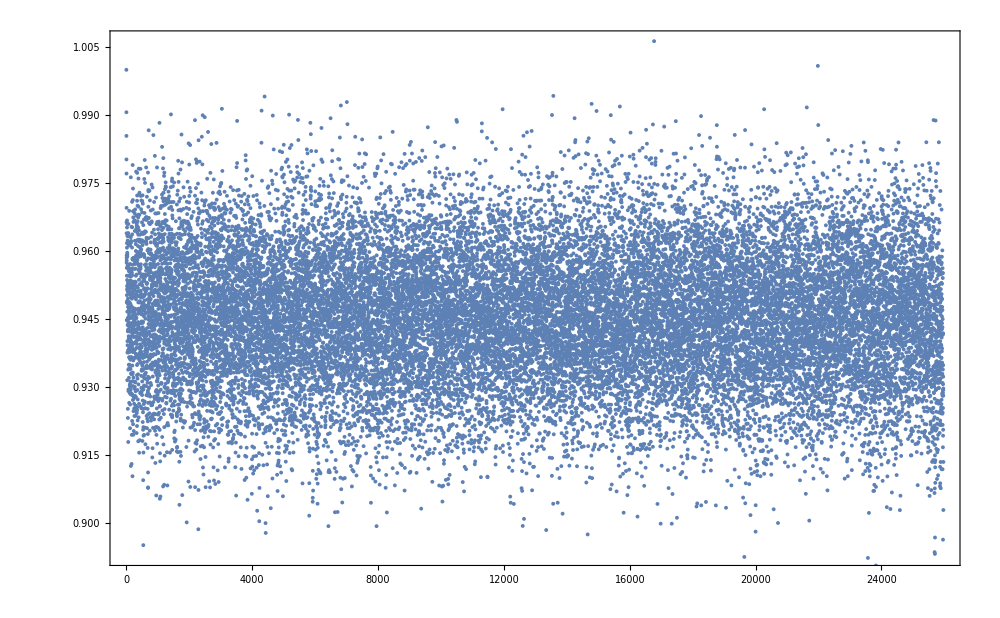

```mathematica
(* Select the result from a single run and plot. Pick any integer between 1 and 50 *)
selectData=1;
rawData = allRawData[[selectData,1]];

ListPlot[rawData]
```

Process Topological Charge Data

Options we provide:
H = -0.0014; Tstart = 0.09; Tend = 0.12; dT = 0.01;
H = -0.0015; Tstart = 0.09; Tend = 0.12; dT = 0.01;
H = -0.0016; Tstart = 0.06; Tend = 0.09; dT = 0.01;
H = -0.0017; Tstart = 0.06; Tend = 0.09; dT = 0.01;
H = -0.0018; Tstart = 0.06; Tend = 0.09; dT = 0.01;
H = -0.0019; Tstart = 0.05; Tend = 0.08; dT = 0.01;
H = -0.002; Tstart = 0.05; Tend = 0.08; dT = 0.01;
H = -0.0021; Tstart = 0.03; Tend = 0.06; dT = 0.01;
H = -0.0022; Tstart = 0.02; Tend = 0.04; dT = 0.01;
H = -0.0023; Tstart = 0.02; Tend = 0.04; dT = 0.01;
H = -0.0024; Tstart = 0.009; Tend = 0.013; dT = 0.001;

H=-0.00255;Tstart=0.001;Tend=0.0013;dT=0.0001;

```mathematica
(* To process raw data, change parameters here to appropriate values. relDir defines folder where data is saved. *)
DMI=0.02;ED="0.0";PMA="0.0";tFree = 2.0;
relDirRaw = ParentDirectory[]<>"/data/raw-collapse-data-skyrmion/";
filePrefix=relDirRaw<>"topological_charge_during_dynamics";

(*****************************************************)
(* Must change the following range of temperatures to the ones evaluated in thermal collapse. The temperature range may vary for different magnetic fields. *)
H=-0.00257;Tstart=0.0003;Tend=0.0006;dT=0.0001;
Trange = Range[Tstart,Tend,dT];
(*****************************************************)

(* Determine the times at which collapse. This takes a while, which is why it is suggested to process the data and save the results, {T1, {t1, t2, t3}, ...} in a file so that you do not need to process the same data every time. *)
allCollapseTimes = {#,getCollapseTimes[filePrefix,#,H,DMI,ED,PMA]}&/@Trange;
```

```mathematica
(* Get collapse rate from the collapse time data *)
processCollapseTimes[allCollapseTimes]
```

{{3333.33,0.00149247},{2500.,0.00147882},{2000.,0.00150022},{1666.67,0.00150244}}

### ----------------Save list of collapse times -------------------

```mathematica
(* Since imporing thousands of topological charge lists and processing them all takes time, it is advantageous to process them once to extract the collapse time at each run, and save the results to the folder ParentDirectory[]<>"/data/processed-collapse-times" *)
relDirProcessed=ParentDirectory[]<>"/data/processed-collapse-times-skyrmion/";
fileName="collapse_times_H="<>ToString[H]<>"_DDI="<>ToString[ED]<>"_PMA="<>ToString[PMA]<>".csv";

Export[relDirProcessed<>fileName,allCollapseTimes]
```

/home/amel/Documents/pulse_noise_spin_lattice/data/processed-collapse-times-skyrmion/collapse_times_H=-0.00257_DDI=0.0_PMA=0.0.csv

Import and plot collapse times

```mathematica
relDirProcessed=ParentDirectory[]<>"/data/processed-collapse-times-skyrmion/";

(* Original data was only labeled with magnetic field because we did not include PMA and DDI in those calculations. Updated data should use the more versatile fileSuffix below *)
fileNameOLD="collapse-times_H="<>ToString[H]<>".csv";
fileName="collapse_times_H="<>ToString[H]<>"_DDI="<>ToString[ED]<>"_PMA="<>ToString[PMA]<>".csv";

collapseTimes = ToExpression@Import[relDirProcessed<>fileName,"CSV"];
```

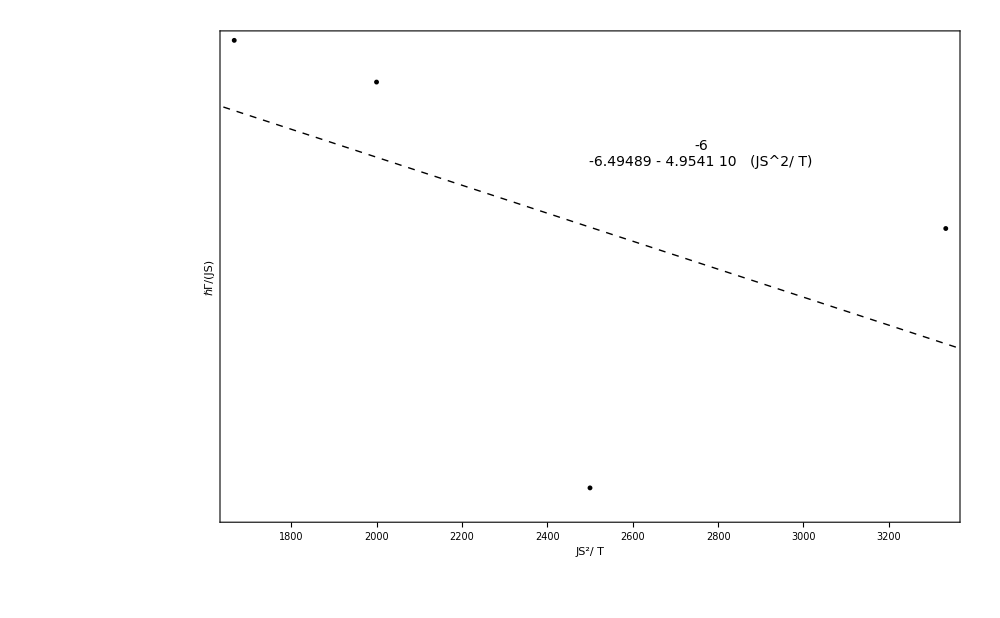

```mathematica
(* 

Plot Γ as a function of 1/T *)
plotGammaVsT[collapseTimes]
```